```mathematica
ZR1=1000;
ZL1=ⅉ*ω*0.001;
ZR2=1000;
ZC2=1/(ⅉ*ω*0.000001);
ZR3=1000;
ZR4=1000;


ZH1=1/(1/ZR1+1/ZL1);

ZH2=1/(1/ZR2+1/ZL2);
```

```mathematica
ZH3=1/(1/ZR3+1/ZR4);
```

```mathematica
Zcelk=ZH1+ZH2+ZH3
```

500+2/(1/1000-(0.+1000. ⅈ)/ω)

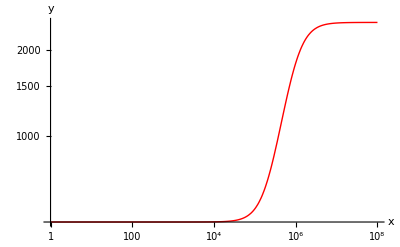

```mathematica
LogLogPlot[Abs[Zcelk],{ω,1,10^8},AxesLabel->{x,y} , PlotStyle->Red]
```